```mathematica
Data2013:= Import["D:\\2013.csv"];
```

```mathematica
Data2014:= Import["D:\\2014.csv"];
```

```mathematica
Data2015:= Import["D:\\2015.csv"];
```

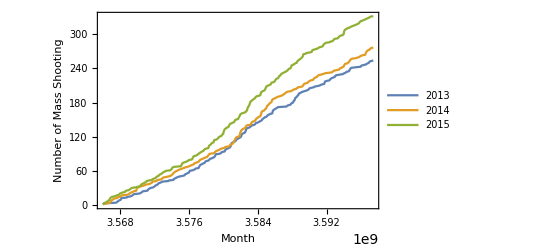

```mathematica
DateListPlot[{Data2013,Data2014,Data2015},PlotLegends->{"2013","2014","2015"},FrameLabel->{"Month","Number of Mass Shooting"}]
```

```mathematica
Data2013linear:=Import["D:\\2013linear.csv"];
```

```mathematica
Data2014linear:=Import["D:\\2014linear.csv"];
```

```mathematica
Data2015linear:=Import["D:\\2015linear.csv"];
```

```mathematica
Model2013=LinearModelFit[Data2013linear,x,x]
```

FittedModel[-23.6611+0.786404 x]

```mathematica
Model2014=LinearModelFit[Data2014linear,x,x]
```

FittedModel[-17.1043+0.812581 x]

```mathematica
Model2015=LinearModelFit[Data2015linear,x,x]
```

FittedModel[-19.3567+0.989794 x]

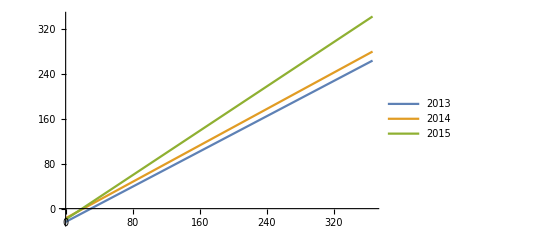

```mathematica
Plot[{Model2013["BestFit"],Model2014["BestFit"],Model2015["BestFit"]},{x,0,366},PlotLegends->{"2013","2014","2015"},FrameLabel->{"Month","Number of Mass Shooting"}]
```

```mathematica
Pred2013 = Model2013["SinglePredictionBands",ConfidenceLevel->0.95]
```

```mathematica
TeXForm[{-23.661053186592877+0.7864043402645833 x-1.9743577636580063 √(61.86858909571006-0.014726684445505777 x+0.00003920892213700429 x^2),-23.661053186592877+0.7864043402645833 x+1.9743577636580063 √(61.86858909571006-0.014726684445505777 x+0.00003920892213700429 x^2)}]
```

\left\{-1.97436 \sqrt{0.0000392089 x^2-0.0147267
   x+61.8686}+0.786404 x-23.6611,1.97436 \sqrt{0.0000392089
   x^2-0.0147267 x+61.8686}+0.786404 x-23.6611\right\}

\left\{-1.97436 \sqrt{0.0000392089 x^2-0.0147267
   x+61.8686}+0.786404 x-23.6611,1.97436 \sqrt{0.0000392089
   x^2-0.0147267 x+61.8686}+0.786404 x-23.6611\right\}

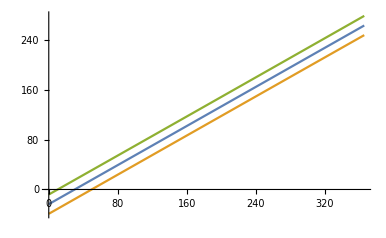

```mathematica
Show[Plot[{Model2013["BestFit"],Pred2013},{x,0,366},FrameLabel->{"Month","Number of Mass Shooting"}]]
```

```mathematica
Pred2014 = Model2014["SinglePredictionBands",ConfidenceLevel->0.95]
```

```mathematica
TeXForm[{-17.104274867676395+0.8125813639537154 x-1.9741004473989796 √(90.78427428818468-0.020117943898980986 x+0.00005171941197194281 x^2),-17.104274867676395+0.8125813639537154 x+1.9741004473989796 √(90.78427428818468-0.020117943898980986 x+0.00005171941197194281 x^2)}]
```

\left\{-1.9741 \sqrt{0.0000517194 x^2-0.0201179
   x+90.7843}+0.812581 x-17.1043,1.9741 \sqrt{0.0000517194
   x^2-0.0201179 x+90.7843}+0.812581 x-17.1043\right\}

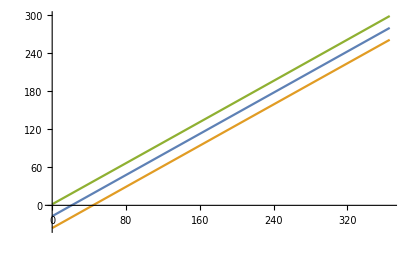

```mathematica
Show[Plot[{Model2014["BestFit"],Pred2014},{x,0,366},FrameLabel->{"Month","Number of Mass Shooting"}]]
```

```mathematica
Pred2015 = Model2015["SinglePredictionBands",ConfidenceLevel->0.95]
```

```mathematica
TeXForm[{-19.35672986938165+0.9897942167210818 x-1.9718962236339095 √(124.0664833810531-0.021189947198326283 x+0.00005779284583686958 x^2),-19.35672986938165+0.9897942167210818 x+1.9718962236339095 √(124.0664833810531-0.021189947198326283 x+0.00005779284583686958 x^2)}]
```

\left\{-1.9719 \sqrt{0.0000577928 x^2-0.0211899
   x+124.066}+0.989794 x-19.3567,1.9719 \sqrt{0.0000577928
   x^2-0.0211899 x+124.066}+0.989794 x-19.3567\right\}

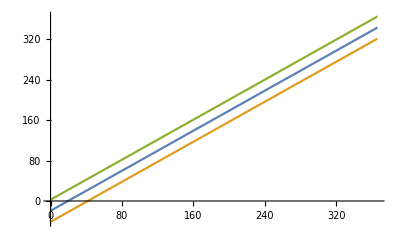

```mathematica
Show[Plot[{Model2015["BestFit"],Pred2015},{x,0,366},FrameLabel->{"Month","Number of Mass Shooting"}]]
```

```mathematica
Model2013["BestFit"]
```

-23.6611+0.786404 x

```mathematica
Model2014["BestFit"]
```

-17.1043+0.812581 x

```mathematica
Model2015["BestFit"]
```

-19.3567+0.989794 x